## init

```mathematica
(*first run this*)
NotebookEvaluate[NotebookDirectory[]<>"main.nb"];
$linux=RGBColor[0.31,0.,0.29];
$lox=RGBColor[0.03,0.15,0.2];
$defaultOptions=Sequence[Background->RGBColor[0.31,0.,0.29],
FontColor->Hue[.5],
Blue,
FontFamily->"Britannic",
FontWeight->Bold,
FontSize->15];
$PinkyTerminal="";
```

## usage

## pinky Interpret

can read file from scripts folder
or pass the program as string
the output is stored in global variable  $PinkyTerminal
then can use DumpModule[$PinkyTerminal] to print it 
or pass number of second as second argument to temporal print it 
this was done to distinguish 
print ()
and println()

```mathematica
PinkyInterPreter["
print '1 - hello'
print \" world\"
print '\n'
println '2 - after break line '
println '3 - new line withou tbreak line '


",2]
```

```mathematica
PinkyInterPreter[
ReadFile["while.pinky"]
];
DumpModule[$PinkyTerminal]
```

The value of the global x is 1
I have access to the local y = 21
I have also access to the global x = 1
i = 1
i = 2
i = 3
i = 4
i = 5
i = 6
i = 7
i = 8
i = 9
i = 10

## debug

print tokens and ast

```mathematica
PinkyShow[
ReadFile["while.pinky"]
,Background->$linux,FontFamily->"Verdana",FontSize->17,Orange]
```

***********************************
Source:
***********************************
x := 0
x := x + 1

println("The value of the global x is " + x)

if 5 ~= 2 then
  y := x + 20
  println("I have access to the local y = " + y)
  println("I have also access to the global x = " + x)
else
  x := y
  println("Error, no local variable " + y)
end

i := 1
while i <= 10 do
  println("i = " + i)
  i := i + 1
end

***********************************
Tokens:
***********************************
(TOK_IDENTIFIER, 'x', 1)
(TOK_ASSIGN, ':=', 1)
(TOK_INTEGER, '0', 1)
(TOK_IDENTIFIER, 'x', 2)
(TOK_ASSIGN, ':=', 2)
(TOK_IDENTIFIER, 'x', 2)
(TOK_PLUS, '+', 2)
(TOK_INTEGER, '1', 2)
(TOK_PRINTLN, 'println', 4)
(TOK_LPAREN, '(', 4)
(TOK_STRING, '"The value of the global x is "', 4)
(TOK_PLUS, '+', 4)
(TOK_IDENTIFIER, 'x', 4)
(TOK_RPAREN, ')', 4)
(TOK_IF, 'if', 6)
(TOK_INTEGER, '5', 6)
(TOK_NE, '~=', 6)
(TOK_INTEGER, '2', 6)
(TOK_THEN, 'then', 6)
(TOK_IDENTIFIER, 'y', 7)
(TOK_ASSIGN, ':=', 7)
(TOK_IDENTIFIER, 'x', 7)
(TOK_PLUS, '+', 7)
(TOK_INTEGER, '20', 7)
(TOK_PRINTLN, 'println', 8)
(TOK_LPAREN, '(', 8)
(TOK_STRING, '"I have access to the local y = "', 8)
(TOK_PLUS, '+', 8)
(TOK_IDENTIFIER, 'y', 8)
(TOK_RPAREN, ')', 8)
(TOK_PRINTLN, 'println', 9)
(TOK_LPAREN, '(', 9)
(TOK_STRING, '"I have also access to the global x = "', 9)
(TOK_PLUS, '+', 9)
(TOK_IDENTIFIER, 'x', 9)
(TOK_RPAREN, ')', 9)
(TOK_ELSE, 'else', 10)
(TOK_IDENTIFIER, 'x', 11)
(TOK_ASSIGN, ':=', 11)
(TOK_IDENTIFIER, 'y', 11)
(TOK_PRINTLN, 'println', 12)
(TOK_LPAREN, '(', 12)
(TOK_STRING, '"Error, no local variable "', 12)
(TOK_PLUS, '+', 12)
(TOK_IDENTIFIER, 'y', 12)
(TOK_RPAREN, ')', 12)
(TOK_END, 'end', 13)
(TOK_IDENTIFIER, 'i', 15)
(TOK_ASSIGN, ':=', 15)
(TOK_INTEGER, '1', 15)
(TOK_WHILE, 'while', 16)
(TOK_IDENTIFIER, 'i', 16)
(TOK_LE, '<=', 16)
(TOK_INTEGER, '10', 16)
(TOK_DO, 'do', 16)
(TOK_PRINTLN, 'println', 17)
(TOK_LPAREN, '(', 17)
(TOK_STRING, '"i = "', 17)
(TOK_PLUS, '+', 17)
(TOK_IDENTIFIER, 'i', 17)
(TOK_RPAREN, ')', 17)
(TOK_IDENTIFIER, 'i', 18)
(TOK_ASSIGN, ':=', 18)
(TOK_IDENTIFIER, 'i', 18)
(TOK_PLUS, '+', 18)
(TOK_INTEGER, '1', 18)
(TOK_END, 'end', 19)

***********************************
AST:
***********************************
Stmts(
  [Assignment(
    Identifier[x], Integer[0]
  )
  , Assignment(
    Identifier[x], BinOp(
      '+',  Identifier[x],  Integer[1]
    )
  )
  , PrintStmt(
    Grouping(
      BinOp(
        '+',  String[The value of the global x is ],  Identifier[x]
      )
    )
     , end=\n
  )
  , IfStmt(
    BinOp(
      '~=',  Integer[5],  Integer[2]
    )
    , then:Stmts(
      [Assignment(
        Identifier[y], BinOp(
          '+',  Identifier[x],  Integer[20]
        )
      )
      , PrintStmt(
        Grouping(
          BinOp(
            '+',  String[I have access to the local y = ],  Identifier[y]
          )
        )
         , end=\n
      )
      , PrintStmt(
        Grouping(
          BinOp(
            '+',  String[I have also access to the global x = ],  Identifier[x]
          )
        )
         , end=\n
      )
      ]
    )
    , else:Stmts(
      [Assignment(
        Identifier[x], Identifier[y]
      )
      , PrintStmt(
        Grouping(
          BinOp(
            '+',  String[Error, no local variable ],  Identifier[y]
          )
        )
         , end=\n
      )
      ]
    )
  )
  , Assignment(
    Identifier[i], Integer[1]
  )
  , WhileStmt(
    BinOp(
      '<=',  Identifier[i],  Integer[10]
    )
    , Stmts(
      [PrintStmt(
        Grouping(
          BinOp(
            '+',  String[i = ],  Identifier[i]
          )
        )
         , end=\n
      )
      , Assignment(
        Identifier[i], BinOp(
          '+',  Identifier[i],  Integer[1]
        )
      )
      ]
    )
  )
  ]
)

## external evaluate

binary code  obtained from Golang  implantation
default registration inside bin directory 
$PinkyRegister

```mathematica
PinkyExternalEvaluate["while.pinky",$defaultOptions]
```

[92m****************************************
[0m[92mSOURCE :[0m
[92m****************************************
[0mx := 0
x := x + 1

println("The value of the global x is " + x)

if 5 ~= 2 then
  y := x + 20
  println("I have access to the local y = " + y)
  println("I have also access to the global x = " + x)
else
  x := y
  println("Error, no local variable " + y)
end

i := 1
while i <= 10 do
  println("i = " + i)
  i := i + 1
end

[92m****************************************
[0m[92mTOKENS :[0m
[92m****************************************
[0m(TOK_IDENTIFIER, 'x', 1)
(TOK_ASSIGN, ':=', 1)
(TOK_INTEGER, '0', 1)
(TOK_IDENTIFIER, 'x', 2)
(TOK_ASSIGN, ':=', 2)
(TOK_IDENTIFIER, 'x', 2)
(TOK_PLUS, '+', 2)
(TOK_INTEGER, '1', 2)
(TOK_PRINTLN, 'println', 4)
(TOK_LPAREN, '(', 4)
(TOK_STRING, '"The value of the global x is "', 4)
(TOK_PLUS, '+', 4)
(TOK_IDENTIFIER, 'x', 4)
(TOK_RPAREN, ')', 4)
(TOK_IF, 'if', 6)
(TOK_INTEGER, '5', 6)
(TOK_NE, '~=', 6)
(TOK_INTEGER, '2', 6)
(TOK_THEN, 'then', 6)
(TOK_IDENTIFIER, 'y', 7)
(TOK_ASSIGN, ':=', 7)
(TOK_IDENTIFIER, 'x', 7)
(TOK_PLUS, '+', 7)
(TOK_INTEGER, '20', 7)
(TOK_PRINTLN, 'println', 8)
(TOK_LPAREN, '(', 8)
(TOK_STRING, '"I have access to the local y = "', 8)
(TOK_PLUS, '+', 8)
(TOK_IDENTIFIER, 'y', 8)
(TOK_RPAREN, ')', 8)
(TOK_PRINTLN, 'println', 9)
(TOK_LPAREN, '(', 9)
(TOK_STRING, '"I have also access to the global x = "', 9)
(TOK_PLUS, '+', 9)
(TOK_IDENTIFIER, 'x', 9)
(TOK_RPAREN, ')', 9)
(TOK_ELSE, 'else', 10)
(TOK_IDENTIFIER, 'x', 11)
(TOK_ASSIGN, ':=', 11)
(TOK_IDENTIFIER, 'y', 11)
(TOK_PRINTLN, 'println', 12)
(TOK_LPAREN, '(', 12)
(TOK_STRING, '"Error, no local variable "', 12)
(TOK_PLUS, '+', 12)
(TOK_IDENTIFIER, 'y', 12)
(TOK_RPAREN, ')', 12)
(TOK_END, 'end', 13)
(TOK_IDENTIFIER, 'i', 15)
(TOK_ASSIGN, ':=', 15)
(TOK_INTEGER, '1', 15)
(TOK_WHILE, 'while', 16)
(TOK_IDENTIFIER, 'i', 16)
(TOK_LE, '<=', 16)
(TOK_INTEGER, '10', 16)
(TOK_DO, 'do', 16)
(TOK_PRINTLN, 'println', 17)
(TOK_LPAREN, '(', 17)
(TOK_STRING, '"i = "', 17)
(TOK_PLUS, '+', 17)
(TOK_IDENTIFIER, 'i', 17)
(TOK_RPAREN, ')', 17)
(TOK_IDENTIFIER, 'i', 18)
(TOK_ASSIGN, ':=', 18)
(TOK_IDENTIFIER, 'i', 18)
(TOK_PLUS, '+', 18)
(TOK_INTEGER, '1', 18)
(TOK_END, 'end', 19)

[92m****************************************
[0m[92mAST :[0m
[92m****************************************
[0mStmts(
  [Assignment(
    Identifier['x'], Integer[0]
  )
  , Assignment(
    Identifier['x'], BinOp(
      '+', Identifier['x'], Integer[1]
    )
  )
  , PrintStmt(
    Grouping(
      BinOp(
        '+', String[The value of the global x is ], Identifier['x']
      )
    )
    , end='\n'
  )
  , IfStmt(
    BinOp(
      '~=', Integer[5], Integer[2]
    )
    , then:Stmts(
      [Assignment(
        Identifier['y'], BinOp(
          '+', Identifier['x'], Integer[20]
        )
      )
      , PrintStmt(
        Grouping(
          BinOp(
            '+', String[I have access to the local y = ], Identifier['y']
          )
        )
        , end='\n'
      )
      , PrintStmt(
        Grouping(
          BinOp(
            '+', String[I have also access to the global x = ], Identifier['x']
          )
        )
        , end='\n'
      )
      ]
    )
    , else:Stmts(
      [Assignment(
        Identifier['x'], Identifier['y']
      )
      , PrintStmt(
        Grouping(
          BinOp(
            '+', String[Error, no local variable ], Identifier['y']
          )
        )
        , end='\n'
      )
      ]
    )
  )
  , Assignment(
    Identifier['i'], Integer[1]
  )
  , WhileStmt(
    BinOp(
      '<=', Identifier['i'], Integer[10]
    )
    ,Stmts(
      [PrintStmt(
        Grouping(
          BinOp(
            '+', String[i = ], Identifier['i']
          )
        )
        , end='\n'
      )
      , Assignment(
        Identifier['i'], BinOp(
          '+', Identifier['i'], Integer[1]
        )
      )
      ]
    )
  )
  ]
)

[92m****************************************
[0m[92mINTERPRETER:[0m
[92m****************************************
[0mThe value of the global x is 1
I have access to the local y = 21
I have also access to the global x = 1
i = 1
i = 2
i = 3
i = 4
i = 5
i = 6
i = 7
i = 8
i = 9
i = 10

## Dragon-Graphics

```mathematica
(*SetSystemOptions["CheckMachineUnderflow"->False];*)

(*Block[{$RecursionLimit=Infinity},*)
PinkyInterPreter["

angle := 0
x := 25
y := 60

func pow(base, exponent)
  ret base ^ exponent
end

func factorial(n)
  res := 1.0
  for i := 1, n do
    res := res * i
  end
  ret res
end

func cos(a)

  a := a % 360
  if a == 0   then ret  1.0 end
  if a == 90  then ret 0.0 end
  if a == 180 then ret -1.0 end
  if a == 270 then ret  0.0 end
  if a == 360 then ret  1.0 end
  ret -99999
end

func sin(a)
a := a % 360
  if a == 0   then ret  0.0 end
  if a == 90  then ret  1.0 end
  if a == 180 then ret  0.0 end
  if a == 270 then ret -1.0 end
  if a == 360 then ret  0.0 end
  ret -99999
end

func dragon(size, level, d)
  if level == 0 then
    x := x - cos(angle) * size
    y := y + sin(angle) * size
    print('{' + x + ',' + y+'},')
  else
    dragon(size / 1.4142135624, level - 1, 1)
    angle := angle - d * 90
    dragon(size / 1.4142135624, level - 1, -1)
  end
end
print '{'
dragon(6, 12, 1)
print '{0,0}}'

"]
```

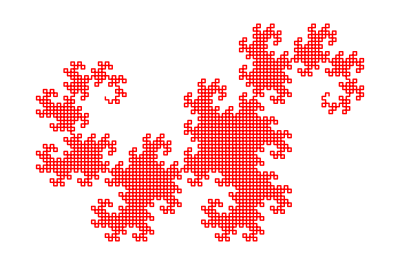

```mathematica
Framed[Graphics[{Red,Thick,Line[Most[ToExpression[$PinkyTerminal]]]}],Background->Black]
```